```mathematica
Clear["`*"]
```

```mathematica
(x-5)^2+(y-5)^2==25
```

(-5+x)^2+(-5+y)^2==25

```mathematica
Solve[(-5+x)^2+(-5+y)^2==25,y]
```

{{y→5-√(10 x-x^2)},{y→5+√(10 x-x^2)}}

```mathematica
a=5-Sqrt[10x-x^2]
```

5-√(10 x-x^2)

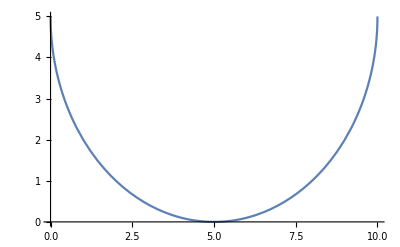

```mathematica
Plot[5-√(10 x-x^2),{x,0,10}]
```

```mathematica
Solve[a==1/2 x,x]
```

{{x→2},{x→10}}

```mathematica
S1=Integrate[a-1/2 x,{x,0,2}]
```

15-25 ArcTan[1/2]

```mathematica
S2=(10^2-Pi*5^2)/4-S1
```

-15+1/4 (100-25 π)+25 ArcTan[1/2]

```mathematica
S=(10 20-2 *Pi* 5^2 )/2-S2
```

15+1/2 (200-50 π)+1/4 (-100+25 π)-25 ArcTan[1/2]

```mathematica
S//Simplify
```

90-(75 π)/4-25 ArcTan[1/2]

```mathematica
N[S,10]
```

19.50394752

```mathematica
Subscript[ℛ, 1]=Rectangle[{0,0},{20,10}];
```

```mathematica
Subscript[ℛ, 2]=Disk[{5,5},5];
Subscript[ℛ, 3]=Disk[{15,5},5];
```

```mathematica
Subscript[ℛ, 4]=Triangle[{{0,0},{20,0},{20,10}}];
```

```mathematica
Subscript[ℛ, 5]=RegionDifference[Subscript[ℛ, 4],RegionUnion[{Subscript[ℛ, 2],Subscript[ℛ, 3]}]];
```

```mathematica
Subscript[ℛ, 6]=RegionIntersection[Subscript[ℛ, 5],Rectangle[{5,0},{20,10}]];
```

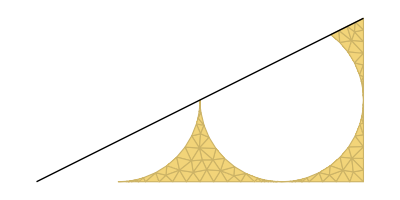

```mathematica
Show[Graphics[{
{HighlightMesh[DiscretizeRegion[Subscript[ℛ, 6]],2]},
{Transparent,EdgeForm[Black],Subscript[ℛ, 1],Subscript[ℛ, 2],Subscript[ℛ, 3]},
Line[{{0,0},{20,10}}]
}]]
```

```mathematica
area=Area[Subscript[ℛ, 6]]//FullSimplify//TraditionalForm
```

90-(75 π)/4-25 cot^-1(2)

```mathematica
N[%,100]
```

19.50394752017122387346903077697896087058964740456375926144646167622349577799003864320933992521310766